```mathematica
D[Sqrt[1+x] u'[x],x]
```

u'[x]/(2 √(1+x))+√(1+x) u''[x]

```mathematica
s1 =NDSolve[{(-0.5/Sqrt[x+1])*u'[x]-Sqrt[x+1]*u''[x]+2*u[x]==50Cos[3x],u[0]==2,u[6]==1},u,{x,0,6}]
```

{{u→InterpolatingFunction[{{0., 6.}}, <>]}}

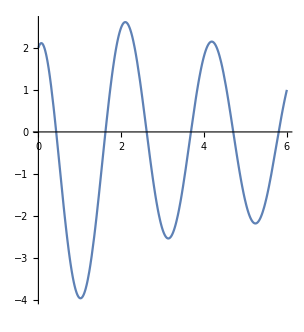

```mathematica
Plot[Evaluate[u[x]] /. s1,{x,0,6},AspectRatio->Automatic]
```

```mathematica
Export["/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test01.txt",Table[{t,(u[t] /. s1)[[1]]},{t,0,6,0.01}],"Table"]
```

/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test01.txt

```mathematica
s2=NDSolve[{(-0.5/Sqrt[x+1])*u'[x]-Sqrt[x+1]*u''[x]+2*u[x]==50Cos[3x],u[0]==2,u'[6]==1},u,{x,0,6}]
```

{{u→InterpolatingFunction[{{0., 6.}}, <>]}}

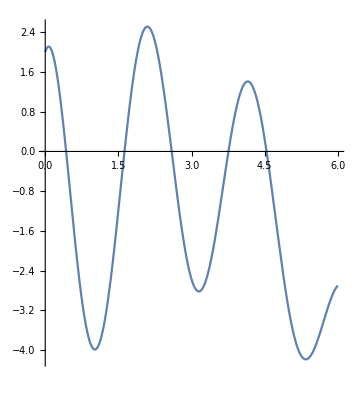

```mathematica
Plot[Evaluate[u[x]] /. s2,{x,0,6},AspectRatio->Automatic]
```

```mathematica
Export["/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test02.txt",Table[{t,(u[t] /. s2)[[1]]},{t,0,6,0.01}],"Table"]
```

/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test02.txt

```mathematica
s3=NDSolve[{(-0.5/Sqrt[x+1])*u'[x]-Sqrt[x+1]*u''[x]+2*u[x]==50Cos[3x],u[0]+3*u'[0]==2,u'[6]==1},u,{x,0,6}]
```

{{u→InterpolatingFunction[{{0., 6.}}, <>]}}

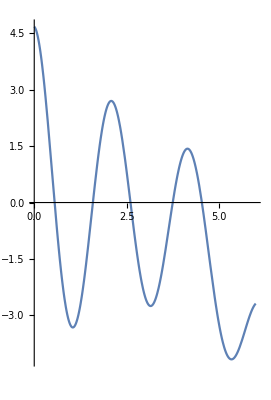

```mathematica
Plot[Evaluate[u[x]] /. s3,{x,0,6},AspectRatio->Automatic]
```

```mathematica
Export["/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test03.txt",Table[{t,(u[t] /. s3)[[1]]},{t,0,6,0.01}],"Table"]
```

/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test03.txt

```mathematica
D[(x^2+1)u'[x],x]
```

2 x u'[x]+(1+x^2) u''[x]

```mathematica
s4=NDSolve[{-(2x)*u'[x]-(x^2+1)*u''[x]+2u'[x]+2*Cos[x/2]*u[x]==x^2,3*u[-Pi]-2*u'[-Pi]==1,u'[Pi]==1},u,{x,-Pi,Pi}]
```

{{u→InterpolatingFunction[{{-3.14159, 3.14159}}, <>]}}

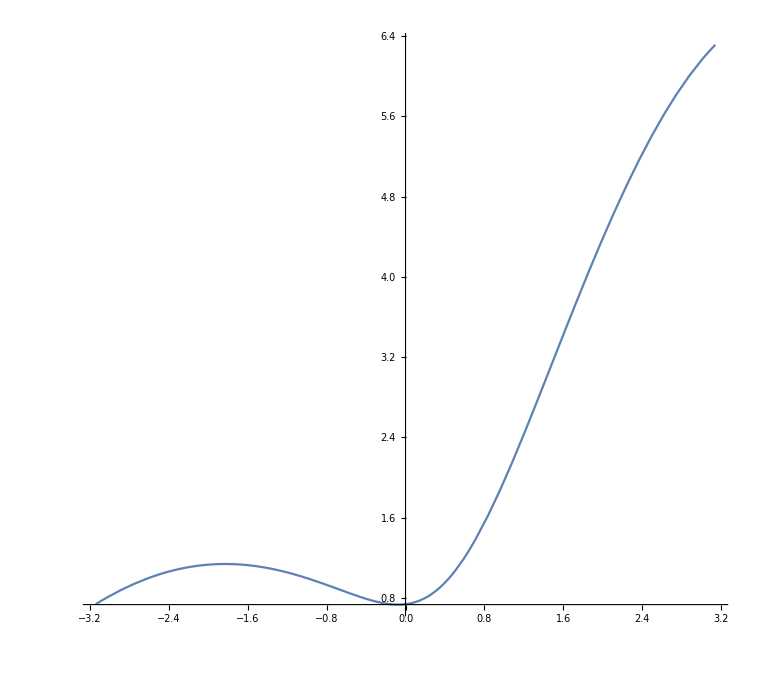

```mathematica
Plot[Evaluate[u[x]] /. s4,{x,-Pi,Pi},AspectRatio->Automatic]
```

```mathematica
Export["/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test04.txt",Table[{t,(u[t] /. s4)[[1]]},{t,-Pi,Pi,0.01}],"Table"]
```

/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/program/fem1d/test04.txt

```mathematica
N[Pi,12]
```

3.14159265359

```mathematica
f[x_]:=Piecewise[{{1,x<1},{2,x < 2},{3,x < 3},{4,x < 4},{5,x < 5},{6,x < 6},{7,x < 7},{8,x < 8},{9,x <9},{10,x <= 10}},0]
```

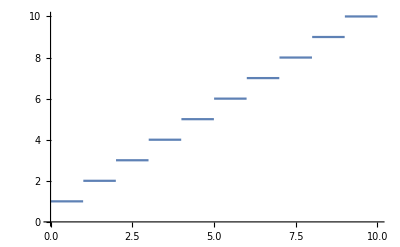

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
g[x_]:=Piecewise[{{(x-1)^2-1/2,x<2},{(x-3)^2-1/2,x<4},{(x-5)^2-1/2,x<6},{(x-7)^2-1/2,x<8},{(x-9)^2-1/2,x≤10}},0]
```

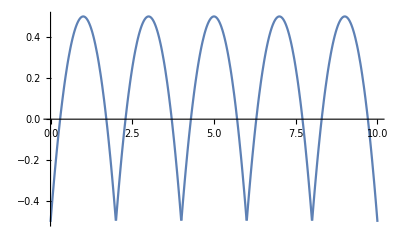

```mathematica
Plot[-g[x],{x,0,10}]
```

```mathematica
s5=NDSolve[{-2x*u'[x]-(x^2+1)*u''[x]+u'[x]-0.1g[x]*u[x]==0.5f[x],3*u[0]-2*u'[0]==1,u'[6]==0},u,{x,0,6}]
```

{{u→InterpolatingFunction[{{0., 6.}}, <>]}}

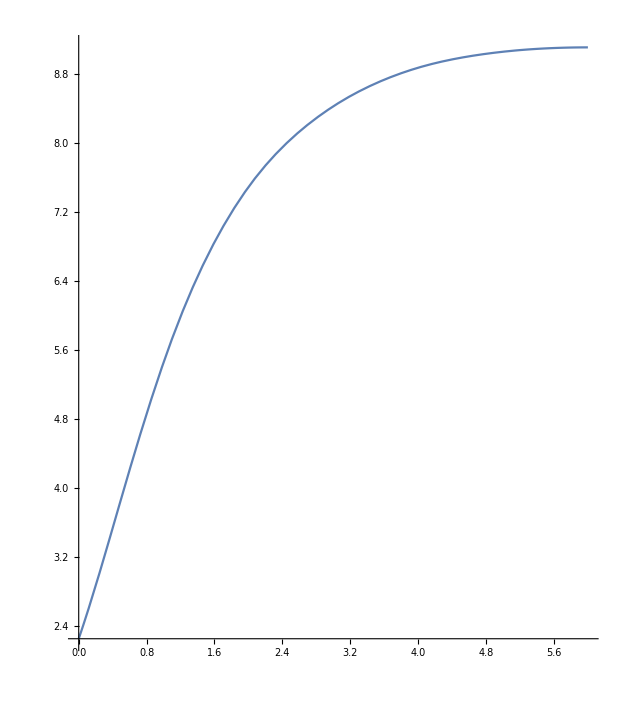

```mathematica
Plot[Evaluate[u[x]] /. s5,{x,0,6},AspectRatio->Automatic]
```

```mathematica
Export["/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/demos/fem1d/test05.txt",Table[{t,(u[t] /. s5)[[1]]},{t,0,6,0.01}],"Table"]
```

/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/demos/fem1d/test05.txt